```mathematica
<<MaTeX`
```

## Первое приближение

```mathematica
ν0 = (3. 10^8)/(670 10^-9)/10^6; (* МГц *)
c = 3 10^8; (* м/c *)
Γ = 6 10^6 /10^6(* МГц *);
vQ = 1200; (* м/c *)
```

```mathematica
ClearAll[f1];
f1[s_, ν_] := f1[s, ν] = NIntegrate[
(1-s/(1 +s+ 4 (ν - ν0(1+ v/c))^2/Γ^2))
1/(1  + 4 (ν - ν0(1- v/c))^2/Γ^2)Exp[- v^2/vQ^2], {v, -4 vQ, + 4 vQ}, MaxRecursion->12];
f1[0, ν0]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

6.30268

```mathematica
β = 1/6; (* β = Subscript[I, out] / Subscript[I, in] *)
κx = -Log[β]/f1[0, ν0] (* c/м *)
```

0.284285

## Оценка κ

```mathematica
kB= 1.38 10^-23;
ℏ = 1.054571817 10^-34;
Na = 6.02 10^23;
R = Na kB;
m = 0.007 / Na;
M = 0.007;
T = 300 + 273;
λ = 671 10^-9;
lx = 0.1;
vQ = √((2 kB T)/m);
Print["тепловая скорость  <v> = ", ScientificForm[vQ, 2], " м/c"];

ClearAll[GetP];
GetP[T_] := 133.32 10^(10.3454 -8345.57/T-8.84 10^-5 T - 0.68106 Log10[T]);

(* оценка κ *)
κx = (1/(vQ √π))(GetP[T]/(kB T))((3π)/8 λ^2)lx;
Print["оценка: κ = ", ScientificForm[κx, 3], " 1/(:043c/c)"]
```

тепловая скорость  <v> = 1.2×10^3 м/c

оценка: κ = 3.07×10^-1 1/(м/c)

```mathematica
κx vQ √π
```

635.435

## Графики

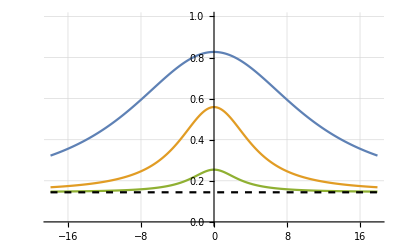

D:\Kami\git_folder\notes_5sem\rqc\saturation_spectr_simulation\frac1.pdf

```mathematica
ϵ =4 10^-8;
image1 = Show[{
DiscretePlot[
{Exp[-κx f1[100, ν0+ν]], Exp[-κx f1[10, ν0+ν]], Exp[-κx f1[1, ν0+ν]], Exp[-κx f1[0, ν0+ν]]}, {ν,- ϵ ν0, ϵ ν0, ϵ ν0 / 100}, 
PlotStyle->{, ,,{Black, Dashed}}, Filling->None, PlotRange->{Automatic, {0, 1}},GridLines->Automatic,
PlotLegends->{MaTeX@"s=100",MaTeX@"s=10",MaTeX@"s=1",MaTeX@"s=0"},
Joined->True, AxesLabel->{MaTeX@"\\nu,\ \\text{MHz}", MaTeX@"\\beta = I_{\\mathrm{out}} / I_{\\mathrm{in}} "}]
}]
Export[NotebookDirectory[]<>"frac1.pdf", image1]
```

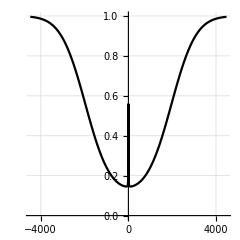

D:\Kami\git_folder\notes_5sem\rqc\saturation_spectr_simulation\frac2.pdf

```mathematica
ϵ =10 10^-6;
image2 = DiscretePlot[
{Exp[-κx f1[10, ν0+ν]]}, {ν,- ϵ ν0, +ϵ ν0, ϵ ν0 / 2000}, PlotRange->{Full, {0, 1}},Filling->None, Joined->True, 
PlotStyle->Black,GridLines->Automatic,
AxesLabel->{MaTeX@"\\nu,\ \\text{MHz}", MaTeX@"{I_{\\mathrm{out}}}/{I_{\\mathrm{in}}},\; \; \; \; \; s=10"}, AspectRatio->1, ImageSize->1.2{200, 200}]
Export[NotebookDirectory[]<>"frac2.pdf", image2]
```

```mathematica
Exp[-κx f1[0, ν0]]
```

0.144064

## Оценка контрастности

Оценим параметр κ из отношения β = I_out / I_in в глубине доплеровского провала.

```mathematica
β = 1/6; (* β = Subscript[I, out] / Subscript[I, in] *)
κx = -Log[β]/f1[0, ν0] (* c/м *)
```

0.284285

```mathematica
ClearAll[GetK];
GetK[β_, s_] :=  (β^(f1[s, ν0]/f1[0, ν0])-β)/(1-β);
```

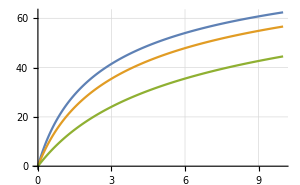

```mathematica
im3 = DiscretePlot[{100GetK[0.5, s], 100GetK[0.3, s], 100GetK[0.1, s]}, {s, 0, 10, 0.01}, Joined->True, Filling->None, (*PlotLabel->"Зависимость контрастности от параметра насыщения", *)(*PlotStyle->{RGBColor[0.,0.57,0.], Thickness[10^-2]}, *)GridLines->Automatic, AxesLabel->{MaTeX["s"], MaTeX["K,\\, \\%"]}, ImageSize->{300,150}, PlotLegends->{MaTeX["\\beta = 0.5"], MaTeX["\\beta = 0.3"], MaTeX["\\beta = 0.1"]}]
```

```mathematica
Export[NotebookDirectory[]<>"K.pdf", im3]
```

D:\Kami\git_folder\notes_5sem\rqc\saturation_spectr_simulation\K.pdf